```mathematica
Omega[d_]:=(2 π^(d/2))/Gamma[d/2];
NV=5;
d=3;
kappa=0.01;

V[rho_]:=Sum[(lambda[i][k])/(i!)(rho-kappa)^i,{i,0,NV}]
dtV[rho_]:=Omega[d]/(2π)^d k^(d+2)/d(1/(k^2+V'[rho,k])+1/(k^2+V'[rho]+2rho V''[rho]))
```

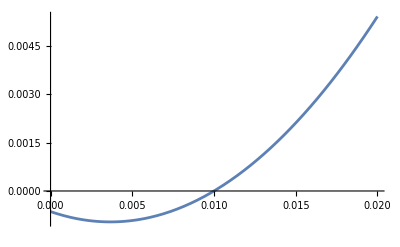

```mathematica
lambdaList=Table[lambda[i],{i,0,NV}];
equationSystem=Join[
Table[lambda[i]'[k]==1/k D[dtV[rho],{rho,i}],{i,0,NV}],
{
lambda[0][0.65]==0.,
lambda[1][0.65]==0.2,
lambda[2][0.65]==60.5
},
Table[lambda[i][0]==0,{i,3,NV}]
]//.rho->kappa;

solution=NDSolve[equationSystem,lambdaList,{k,0.65,0.}];Plot[Evaluate[V[rho]-lambda[0][0]/.solution]//.k->0,{rho,0,0.02}]
```